Задание №1
Найти значение выражения
а) (z̄)_1*z_2   b) (z_1/z_2)^2 c)OverBar[z_1^4]^(1/3)

```mathematica
Subscript[z, 1]=2-2I;
Subscript[z, 2]=1+3I;
```

```mathematica
a=Conjugate[Subscript[z, 1]]*Subscript[z, 2]
```

-4+8 ⅈ

Функция Conjugate [z] принимает комплексное число и возващает число ему сопряженное.

```mathematica
b=(((2-2I)(1-3I))/((1+3I)(1-3I)))^2
```

-12/25+(16 ⅈ)/25

```mathematica
c)Subscript[OverBar[z^4], 1]^(1/3)
```

Найдем значение аргумента числа Z_1

```mathematica
Arg[Subscript[z, 1]]
```

-π/4

Воспользуемся тригонометрической формой записи:

```mathematica
Subscript[Z, 1]=Abs[Subscript[z, 1]] (Cos[-π/4]+I Sin[-π/4])
```

Для возведения в 4-ую степень воспользуемся формулой Муавра:

```mathematica
Subscript[Z, 1]^4=Abs[Subscript[z, 1]]^4(Cos[4*(-π/4)]+I Sin[4(-π/4)])
```

-64

Получили Z_1^4 равным (-64 + 0 i). Сопряженное будет равно (-64 - 0 i).
Затем чтобы найти корень 3-ий степени воспользуемся следующей формулой:

```mathematica
c=Abs[64]^(1/3)(Cos[(-π+2π k)/3]-I Sin[(-π+2π k)/3]) , где k={0,1,2}
```

В итоге получаем ответ:

```mathematica
Subscript[с, 1]=4 (Cos[(-π+2π 0)/3]-I Sin[(-π+2π 0)/3])
```

4 (1/2+(ⅈ √3)/2)

```mathematica
Subscript[с, 2]=4 (Cos[(-π+2π)/3]-I Sin[(-π+2π)/3])
```

4 (1/2-(ⅈ √3)/2)

```mathematica
Subscript[с, 3]=4 (Cos[(-π+2π 2)/3]-I Sin[(-π+2π 2)/3])
```

-4

Получили 3 корня:

```mathematica
c={ReIm[4 (1/2+(ⅈ √3)/2)],ReIm[4 (1/2-(ⅈ √3)/2)],ReIm[-4]};
```

Функция ReIm [z] принимает комплексное число и возвращает точку { Re[z], Im[z] }

Изобразим их на плоскости:

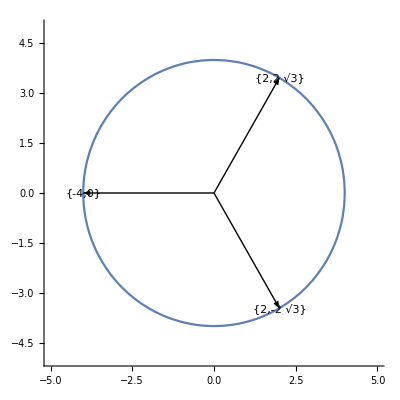

```mathematica
Show[ContourPlot[{x^2+y^2==Abs[-4]^2},{x,-5,5},{y,-5,5},Axes->True,Frame->False],Graphics[{Text[#,#],Arrow[{{0,0},#}]}&/@#,Point@#     ]&@c         ]
```